## 449 Homework #3

```mathematica
<<"http://www.physics.wisc.edu/~tgwalker/448defs.m"
```

### 1) Townsend 10.2

a) ⟨E⟩=

```mathematica
16/25(-1/2)+9/25(-1/(2 2^2))
```

-73/200

⟨L^2⟩=16/25 0+9/25 2=18/25, ⟨L_z⟩=16/25 0+9/25 1=9/25

b) ψ(t)=4/5 100 ⅇ^(ⅈ 1/2 t^2)+(3ⅈ)/5 100 ⅇ^(ⅈ 1/8 t^2)   None of the three expectation values vary with time because the operators commute with the Hamiltonian

### 2) Townsend 10.7

rescale Sch. Eq. for arbitary z:  (m a_z^2)/ℏ^2(Z e^2)/a_z=1→ a_z=ℏ^2/(Z m e^2)=a_0/Z→ P_nl^z(r)=N_z P_nl(Z r) where N_z is a normalization factor. Check that N_z=√Z.  The wavefunction is unchanged immediately after the charge is changed, but then changes with time after that, ψ(t)=∑_n ψ_n nψ(0)ⅇ^(ⅈ Z^2/(2 n^2)t). So prob of finding electron in the new n=0 state is

```mathematica
Integrate[Subscript[P, 1,0][s](√2 Subscript[P, 1,0][2s]),{s,0,∞}]^2
```

512/729

```mathematica
%//N
```

0.702332

### 3) Townsend 10.13

expectation value of any  operator is zero when the system is in an energy eigenstate

[H,r_i p_i]=r_i[H,p_i]+[H,r_i]p_i=r_i(ⅈ ℏ (∂_i V))+1/(2m)[p_i^2,r_i]p_i=r_i(ⅈ ℏ (∂_i V))+1/(2m)(-ⅈ ℏ 2 p_i)p_i
E[H,r·p]E=E-ⅈ ℏ r·(∇V)-2ⅈ p^2/(2m)E=0→ ⟨K⟩=-1/2⟨r·(∇V)⟩

### 4) Townsend 10.19

a) S^2=(S_1+S_2)^2=S_1^2+S_2^2+2 S_1·S_2→ S_1·S_2=(s(s+1)-2(3/4))/2=Piecewise[{{-3/4, s=0}, {1/4, s=1}}]

thus for s=1 the potential is V_a (the bigger sphere) and for s=0 it is V_b (the smaller sphere).  The bigger sphere has the lower ground state energy so the ground state wavefunction is (√(2/a)sin( π r/a))/r Y_00 1 m_S which is triply degenerate.
b)  The first excited state of the particle in a sphere is the lowest state with l=1.  From our particle in a sphere calcs, the energy of that state is 20.19/π^2 times that of the ground state.  So the first excited triplet state has E=20.19 ℏ^2/(2 m a^2) whereas the lowest singlet has E=π^2 ℏ^2/(2 m b^2).  So the first excited state is the lowest singlet state if π^2 ℏ^2/(2 m b^2)<20.19 ℏ^2/(2 m a^2)→ b>π/(√20.19)a=0.7 a

### 5) What is the degeneracy and parity of the 17/2 ℏω energy levels of the 3 dimensional isotropic harmonic oscillator? Calculate the wavefunction of the l=5 state.

2k+l=14/2=7 so l is odd and the parity is odd.  l=1,3,5,7 so the degeneracy is 3+7+11+15=36.

The l=5 state has k=1 so that (2k+l+3/2)ℏω=17/2 ℏω.  This state is a supersymmetric partner of the k=0, l=6 state, which has the wavefunction r^7 ⅇ^(-r^2/2).  So the wavefunction for l=5 is:

```mathematica
(A†)_l_@f_:=-D[f, r]+(r-(l+1)/r)f;
(A†)_5@(r^7 ⅇ^(-r^2/2))//Simplify
```

ⅇ^(-r^2/2) r^6 (-13+2 r^2)

### 6) Townsend 12.2

a) spin 0 (symmetric orbital): gnd state n_1 n_2=00, E_00=2 1/2 ℏ ω, 1st excited |10⟩+|01⟩, E_01=(3/2+1/2=2)ℏω
spin1 (antisymmetric orbital) gnd state  |10⟩-|01⟩, 2ℏω, 1st excited states |20⟩-|02⟩, 2ℏω (there is no 11-11 state)

b)  For the triplet states, Ψ(x,x)=0 so the particles are never at the same place.  For the singlet states,Ψ(x,x)≠0  so the energy of the singlet states is lowered compared to the triplet states.

```mathematica
Det[{{1, 1}, {1/2, -1/2}}]
```

-1

### 7) Townsend 12.4

scaling length (m a^2)/ℏ^2 b a^4=1→ a=(ℏ^2/(m b))^(1/6), energy scale ℏ^2/(m a^2)=((ℏ^4 b)/m^2)^(1/3)=(b^(1/3)(ℏ^2/m))^(2/3)

```mathematica
$Assumptions=z>0;psi=(ⅇ^(-z s^2))/(Integrate[ⅇ^(-2z s^2),{s,-∞,∞}]^(1/2))
```

ⅇ^(-s^2 z) (2/π)^(1/4) z^(1/4)

```mathematica
Integrate[psi (-1/2 D[psi, s,s]+s^4 psi),{s,-∞,∞}]
```

3/(16 z^2)+z/2

```mathematica
Minimize[{%,z>0},z]
```

{(3 3^(1/3))/(4 2^(2/3)),{z→3^(1/3)/2^(2/3)}}

```mathematica
%//N
```

{0.68142,{z→0.90856}}

```mathematica
0.6814202223120523 2^(2/3)
```

1.08169

2% too large

### 8) Townsend 12.6

```mathematica
H=p^2/(2m)+m g z, scaling length (m^2 a^2)/ℏ^2 g a=1-> a=(ℏ^2/(m^2 g))^(1/3), Subscript[E, s]=ℏ^2/(m a^2)=(ℏ^2 m g^2)^(1/3)
```

sketch something like

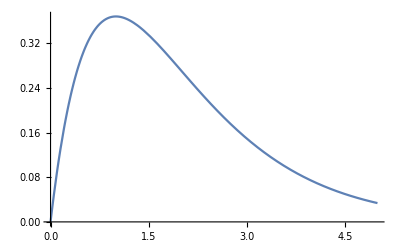

```mathematica
Plot[z ⅇ^-z,{z,0,5}]
```

Any function of that shape will do, but let’s be a little fancy.  At large z, κ=√(2m(V-E)/ℏ^2)~z^(1/2) so ψ~ ⅇ^(-z^(3/2)) so guess ψ=s ⅇ^(-α s^(3/2))

```mathematica
$Assumptions=α>0;psi=(s Exp[-α s^(3/2)])/(Integrate[(s Exp[-α s^(3/2)])^2,{s,0,∞}]^(1/2))
```

(√6 ⅇ^(-s^(3/2) α) s)/(√(1/α^2))

```mathematica
ℰ=Integrate[psi (-1/2 D[psi, s,s] +s psi),{s,0,∞}]
```

((8+9 α^2) Gamma[8/3])/(8 2^(2/3) α^(2/3))

```mathematica
Minimize[{%,α>0},α]
```

{(3 3^(2/3) Gamma[8/3])/(4 2^(1/3)),{α→2/3}}

```mathematica
%//N
```

{1.863,{α→0.666667}}

```mathematica
ps[s_]=(With[{ϵ=1.85575},NDSolve[{-1/2 ψ''[s]+s ψ[s]==ϵ ψ[s],ψ[10]==1,ψ'[10]==-1},ψ[s],{s,10,0}]] //Tr)⟦2⟧;ps[0]/ps'[0]
```

7.07916×10^-6

```mathematica
<<"http://www.physics.wisc.edu/~tgwalker/448defs.m"
```

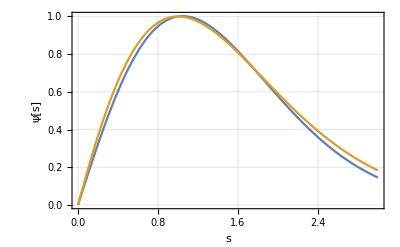

```mathematica
ThadPlot[Plot[{ps[s]/ps[1],(s Exp[-α s^(3/2)])/Exp[-α ]/.α->2/3},{s,0,3}],{"s","ψ[s]"}]
```

c) using our variational function

```mathematica
Integrate[s psi^2/.α->2/3,{s,0,∞}]
```

(5 Gamma[5/3])/(2 6^(1/3))

```mathematica
%//N
```

1.242

“exact” answer

```mathematica
NIntegrate[s ps[s]^2,{s,0,10}]/NIntegrate[ ps[s]^2,{s,0,10}]
```

1.23716

often expectation values of variational functions are not as accurate as the energy estimates are.  Here, since s is the potential energy, we likely get a better result than would be obtained for some other operator not so closely related to the energy.